```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["Spins_T_1_h_50_minusK_60_G_30_theta_0.12566370614359174.dat","Table"];
data1=Rest[data](* first row dropped *);
```

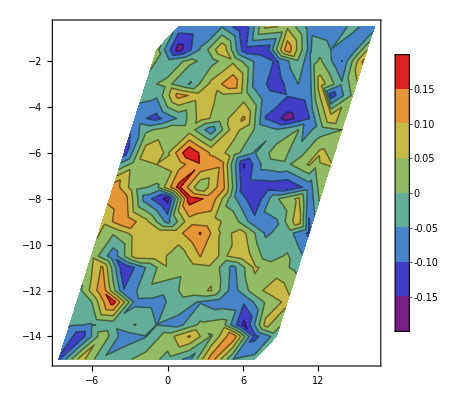

```mathematica
data2=Table[{data1[[i]][[2]],data1[[i]][[3]],data1[[i]][[6]]},{i,1,200,1}];
ListContourPlot[data2,PlotLegends->Automatic,ColorFunction->"Rainbow"]
```

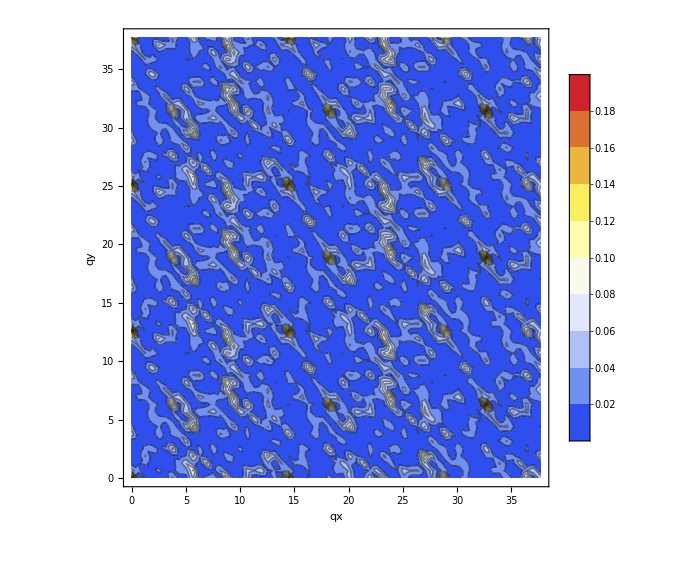

structure-facor.jpg

```mathematica
SetDirectory[NotebookDirectory[]];
data=Import["Strfac_T_1_h_50_minusK_60_G_30.dat","Table"];
data1=Rest[data](* first row dropped *);
data2=Table[{data1[[i]][[1]],data1[[i]][[2]],data1[[i]][[4]]},{i,1,61*61,1}];
pl=ListContourPlot[data2,PlotLegends->Automatic,ColorFunction->"TemperatureMap",InterpolationOrder->16, Frame->True,FrameLabel->{"qx","qy"},ImageSize->Large,PlotRange->All]
Export["structure-facor.jpg",pl]
```

```mathematica
pl1=ListPlot3D[data2,PlotLegends->Automatic,ColorFunction->"TemperatureMap",InterpolationOrder->16,Axes->True,AxesLabel->{"qx","qy","Str"},ImageSize->Large,PlotRange->All]
Export["structure-facor1.jpg",pl1]
```

-Graphics3D-

structure-facor1.jpg

```mathematica
data2
```

{{0.,0.,4.13905},{0.,0.628319,5.23429},{0.,1.25664,6.58524},{0.,1.88496,4.92271},{0.,2.51327,4.4488},{0.,3.14159,1.2822},{0.,3.76991,7.48861},{0.,4.39823,1.01435},{0.,5.02655,1.92155},{0.,5.65487,1.21183},{0.,6.28319,0.541864}}